## Combi - Example sheet x

Problem 1
a)

```mathematica
Clear[a]
Clear[b]
Clear[c]
a=0.1;
b=1;
c=0.5;
d=1;
dS[S_,P_,k_]:=b(S-P)-c S - (S(P+S))/k-a S P 
dP[S_,P_,k_]:=-c P - (P(P+S))/k+a S P
solution[k_]:=Solve[{dS[s,p,k]==0,dP[s,p,k]==0},{s,p}];
s[k_]:=s/.solution[k]
p[k_]:=p/.solution[k]
s[k]
p[k]
s0=s[30];
p0=p[30];
(*kc/.Solve[{p[kc]==0},kc][[1]]
a=1;
b=2;
c=1.5;
Kmin=b/(a(b-c))-10;
Kmax=b/(a(b-c))+10;
Show[Plot[s[K],{K,Kmin,Kmax}],Plot[p[K],{K,Kmin,Kmax}],PlotRange->All]
```

```mathematica
b)
```

```mathematica
c=2.1;
StreamPlot[{v,-c v -u(1-u)},{u,-0.5,1.5},{v,-1,1}]
ParametricPlot[{v[t], -c v[t] - u[t](1-u[t])},{t,-0.5,1.5}]
```

```mathematica
c)
```

```mathematica
a=0.1;
b=1;
c=0.5;
k=30;
d=1;
L=100;
timeSteps=6000;
S=Table[0,{i,1,100},{j,1,timeSteps}];
P=Table[0,{i,1,100},{j,1,timeSteps}];
S[[1]][[1]]=10;
P[[1]][[1]]=5;
dt=0.01;

laplacian[func_,x_,t_,L_]:= func[[Mod[(x-1)-1,L]+1]][[t-1]]+func[[Mod[(x+1)-1,L]+1]][[t-1]]-2*func[[x]][[t-1]];

For[t=2,t≤timeSteps,t++,For[i=1,i≤L,i++,{S[[t]]=S[[t-1]]+(b(S[[t-1]]+P[[t-1]])-c S[[t-1]]-(S[[t-1]](P[[t-1]]+S[[t-1]]))/k-a S[[t-1]]P[[t-1]]+d(laplacian[S,i,t,L]))dt,P[[t]]=P[[t-1]]+(-c P[[t-1]]-(P[[t-1]](P[[t-1]]+S[[t-1]]))/k+a S[[t-1]]P[[t-1]]+d(laplacian[P,i,t,L]))dt}]]
```

```mathematica
ListDensityPlot[S]
```

```mathematica
ListDensityPlot[P]
```

```mathematica
Show[ListPlot[P[[50]]],ListPlot[S[[50]]],PlotRange->All]
```

```mathematica
N[5/3.5]
```

Problem 2
a)

```mathematica
s=N[(81+Sqrt[81^2-49*81])/49]
Show[Plot[d^2-162/49 d+81/49,{d,-2,4}],ListPlot[{{s,0}},PlotStyle->Red]]
```

```mathematica
b)
```

```mathematica
a = 3; 
b = 8; 
L = 128; 
transientTime=25;
timeSteps = 1000; 
dVals = {2.3,3,5,9}; 
d=3;
dt = 0.01; 
uCurr= Table[a(1+RandomReal[{-0.1,0.1}]), {i, 1, L}, {j, 1, L}]; 
vCurr = Table[b/a(1+RandomReal[{-0.1,0.1}]), {i, 1, L}, {j, 1, L}];
uNext=Table[0,{i,1,L},{j,1,L}];
vNext=Table[0,{i,1,L},{j,1,L}];
uTransient=Table[0,{i,1,L},{j,1,L}];
vTransient=Table[0,{i,1,L},{j,1,L}];

laplace[func_,x_,y_,t_,L_]:=func[[Mod[(x - 1), L,1]]][[y]] + 
         func[[Mod[(x + 1), L,1]]][[y]] + 
         func[[x]][[Mod[(y - 1), L,1]]] + 
         func[[x]][[Mod[(y + 1), L,1]]] - 
         4*func[[x]][[y]];


For[t = 2, t <= timeSteps, t++,{For[x = 1, x <= L, x++, 
   For[y = 1, y <= L, y++, {uNext[[x]][[y]]=uCurr[[x]][[y]]+(a-(b+1)uCurr[[x]][[y]]+(uCurr[[x]][[y]])^2vCurr[[x]][[y]]+laplace[uCurr,x,y,t,L])dt, 
     vNext[[x]][[y]]=vCurr[[x]][[y]]+(b uCurr[[x]][[y]]-(uCurr[[x]][[y]])^2vCurr[[x]][[y]]+d laplace[vCurr,x,y,t,L]) dt}]],vCurr=vNext,uCurr=uNext,If[t==transientTime,{vTransient=vCurr,uTransient=uCurr}]}]
```

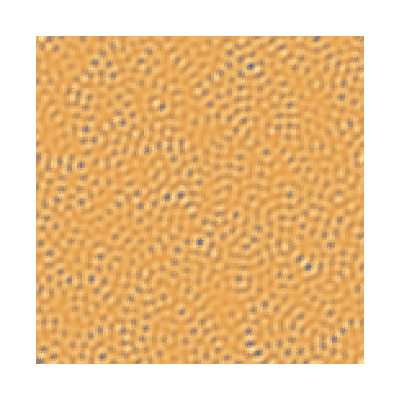

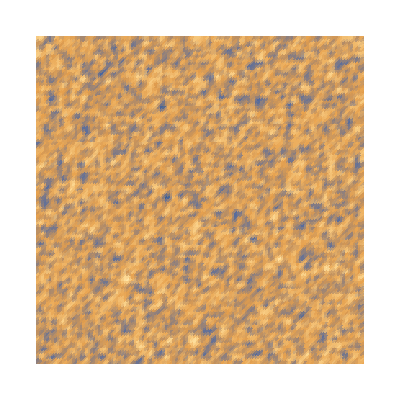

```mathematica
ListDensityPlot[uCurr,Frame->False]
ListDensityPlot[uTransient, Frame->False]
```

```mathematica
i
```

1

```mathematica
uCurr[[1]]
```

{{3.30803,3.03487,3.30431,3.17601,3.28381,2.75303,116,3.00005,3.26371,2.91903,2.94937,3.05991,3.25629},126,{1}}
 |  |  |  |

```mathematica
d
```

2.3

```mathematica
L=128
```

```mathematica
Mod[(L+ 1), L,1]
```

1

```mathematica
Mod[(L + 1) - 1, L] + 1
```

```mathematica
t
```

1001

```mathematica
tmp=uCurr
tmp2=uTransient
```

{{3.19817,3.68549,3.95901,4.08377,3.7083,2.5436,116,2.89447,3.67552,3.95053,3.90913,3.19196,2.74155},126,{1}}
 |  |  |  |

{{2.84273,3.2652,3.42168,3.13811,3.08167,3.081,116,2.97583,3.07902,3.01612,3.24524,3.11297,3.07685},126,{1}}
 |  |  |  |

{{3.46445,3.70976,3.8345,3.54529,2.37112,2.42022,3.63468,115,1.89026,1.36055,1.81548,2.54234,2.65149,2.91195},126,{1}}
 |  |  |  |

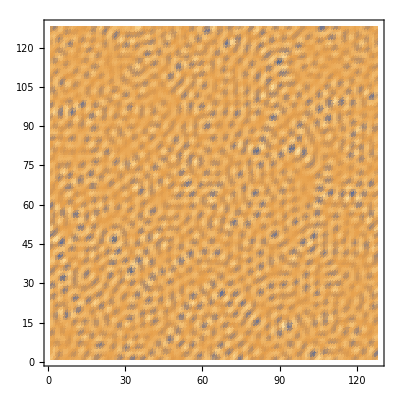

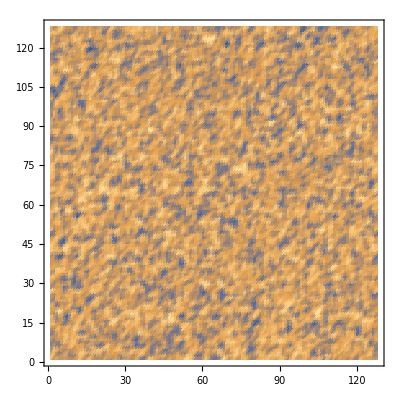

```mathematica
Show[ListDensityPlot[uCurr]]
ListDensityPlot[uTransient]
```

```mathematica
u=Table[a(1+RandomReal[{-0.1,0.1}]),{t,1,timeSteps},{i,1,L},{j,1,L}];
v=Table[b/a(1+RandomReal[{-0.1,0.1}]),{t,1,timeSteps},{i,1,L},{j,1,L}];
laplace[func_,x_,y_,t_,L_]:=func[[t-1]][[Mod[(x - 1) - 1, L] + 1]][[y]] + 
         func[[t-1]][[Mod[(x + 1) - 1, L] + 1]][[y]] + 
         func[[t-1]][[x]][[Mod[(y - 1) - 1, L] + 1]] + 
         func[[t-1]][[x]][[Mod[(y + 1) - 1, L] + 1]] - 
         4*func[[t-1]][[x]][[y]];


For[t = 2, t <= timeSteps, t++,For[x = 1, x <= L, x++, 
   For[y = 1, y <= L, y++, {u[[t]][[x]][[y]]=u[[t-1]][[x]][[y]]+(a-(b-1)u[[t-1]][[x]][[y]]+(u[[t-1]][[x]][[y]])^2v[[t-1]][[x]][[y]]+laplace[u,x,y,t,L])dt, 
     v[[t]][[x]][[y]]=v[[t-1]][[x]][[y]]+(b u[[t-1]][[x]][[y]]-(u[[t-1]][[x]][[y]])^2v[[t-1]][[x]][[y]]+d laplace[v,x,y,t,L]) dt}]]]
```

```mathematica
Simplify[(b-c-(P+2S)/K-a P)*(-c-(2P+S)/K+a S)-(-P/K+a P)(b-S/K-a S)]
```

(b-c) (-a c K+b (-1+a K))

```mathematica
P=K(b-c)-b/a
```

-b/a+(b-c) K

```mathematica
S=b/a
```

b/a